```mathematica
D[u[X],{X,2}]-2 (m-3/(2*Cosh[X]^2)) u[X]==0//TraditionalForm
```

u''(X)-2 u(X) (m-(3 sech^2(X))/2)==0

```mathematica
equation[m_]:=D[u[x,τ],τ]==D[u[x,τ],{x,2}]-(m-6/(1*Cosh[x]^2)) u[x,τ]-u[x,τ]^3;
```

```mathematica
solution[m_,τm_,L_,initialCondition_]:=NDSolve[{equation[m],u[-L,τ]==0,u[L,τ]==0,initialCondition},u[x,τ],{x,-L,L},{τ,0,τm},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->5 L}}]
```

```mathematica
tmaxfn[m_,ϵ_]:=10*8/((0.5-m)^2+ϵ)^(1/2);
ϵ=10^-6;
listNorm2=Table[{m,(NIntegrate[u[x,τ]^2/.solution[m,tmaxfn[m,ϵ],30,u[x,0]==0.2 Exp[-x^2]]/.τ->tmaxfn[m,ϵ],{x,-10,10}]/20)^(1/2)},{m,3,4.5,0.005}]/.{x_,{y_}}->{x,y};
fit=FindFit[listNorm2,If[m≥m0,0,A ((m0-m)^2+ϵ)^(1/4)],{A,{m0,4}},m]
```

{A→0.321477,m0→3.9985}

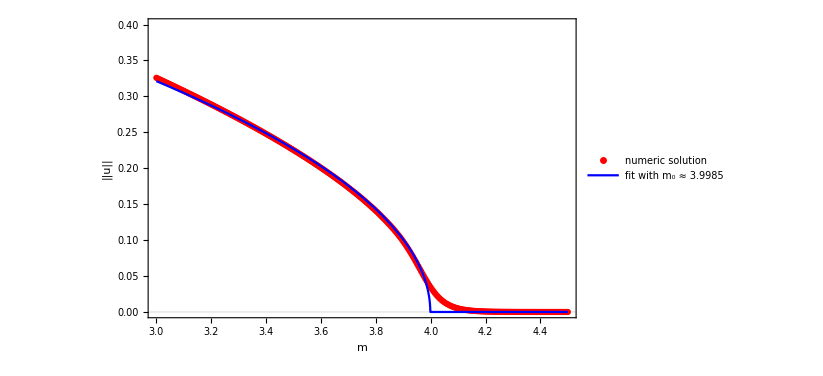

```mathematica
Show[{ListPlot[listNorm2,PlotStyle->Red,PlotTheme->"Scientific",PlotRange-> {0,0.4},Axes->None,FrameTicksStyle->Directive[{Black,10}],FrameLabel->{Style["m",16],Row[{"||",Style["u",16,Italic],"||"}]},PlotLegends->Placed[PointLegend[{Style["numeric solution",12,FontFamily->"Times"]}],Scaled[{0.77,0.77}]]],Plot[If[m>m0,0,A (m0-m)^0.5]/.fit,{m,3,4.5},PlotStyle->{Blue},PlotLegends->Placed[LineLegend[{Style[Row[{" fit with \!\(\*SubscriptBox[\(m\), \(0\)]\) ≈ ",NumberForm[fit[[2,2]],{5,4}]}],12,FontFamily->"Times"]}],Scaled[{0.75,0.6}]]]},ImageSize->400]
```

```mathematica
listNorm2
```

{{3.,0.325868},{3.005,0.324976},{3.01,0.324083},{3.015,0.323188},{3.02,0.322292},{3.025,0.321394},{3.03,0.320494},{3.035,0.319593},{3.04,0.318689},{3.045,0.317785},{3.05,0.316878},{3.055,0.31597},{3.06,0.31506},{3.065,0.314148},{3.07,0.313235},{3.075,0.312319},{3.08,0.311402},{3.085,0.310483},{3.09,0.309562},{3.095,0.30864},{3.1,0.307715},{3.105,0.30679},{3.11,0.305861},{3.115,0.304931},{3.12,0.303999},{3.125,0.303065},{3.13,0.302128},{3.135,0.30119},{3.14,0.300248},{3.145,0.299305},{3.15,0.29836},{3.155,0.297414},{3.16,0.296465},{3.165,0.295514},{3.17,0.29456},{3.175,0.293605},{3.18,0.292647},{3.185,0.291688},{3.19,0.290725},{3.195,0.289761},{3.2,0.288794},{3.205,0.287825},{3.21,0.286853},{3.215,0.28588},{3.22,0.284903},{3.225,0.283924},{3.23,0.282943},{3.235,0.281959},{3.24,0.280973},{3.245,0.279984},{3.25,0.278993},{3.255,0.277999},{3.26,0.277002},{3.265,0.276003},{3.27,0.275001},{3.275,0.273996},{3.28,0.272988},{3.285,0.271978},{3.29,0.270964},{3.295,0.269948},{3.3,0.268929},{3.305,0.267907},{3.31,0.266882},{3.315,0.265854},{3.32,0.264823},{3.325,0.263789},{3.33,0.262752},{3.335,0.261712},{3.34,0.260668},{3.345,0.259621},{3.35,0.258571},{3.355,0.257518},{3.36,0.256461},{3.365,0.255401},{3.37,0.254337},{3.375,0.25327},{3.38,0.252199},{3.385,0.251125},{3.39,0.250047},{3.395,0.248965},{3.4,0.24788},{3.405,0.246791},{3.41,0.245698},{3.415,0.244601},{3.42,0.2435},{3.425,0.242395},{3.43,0.241286},{3.435,0.240172},{3.44,0.239055},{3.445,0.237933},{3.45,0.236808},{3.455,0.235678},{3.46,0.234545},{3.465,0.233405},{3.47,0.232262},{3.475,0.231114},{3.48,0.229961},{3.485,0.228803},{3.49,0.22764},{3.495,0.226473},{3.5,0.225301},{3.505,0.224123},{3.51,0.22294},{3.515,0.221747},{3.52,0.220558},{3.525,0.21936},{3.53,0.218156},{3.535,0.216947},{3.54,0.215729},{3.545,0.214506},{3.55,0.213276},{3.555,0.212041},{3.56,0.210809},{3.565,0.209563},{3.57,0.208312},{3.575,0.207056},{3.58,0.20579},{3.585,0.204517},{3.59,0.203234},{3.595,0.20195},{3.6,0.200657},{3.605,0.19936},{3.61,0.198053},{3.615,0.196733},{3.62,0.195398},{3.625,0.194084},{3.63,0.192756},{3.635,0.191408},{3.64,0.190043},{3.645,0.188684},{3.65,0.18731},{3.655,0.185931},{3.66,0.184538},{3.665,0.183161},{3.67,0.181756},{3.675,0.180336},{3.68,0.178909},{3.685,0.177469},{3.69,0.175997},{3.695,0.174535},{3.7,0.173062},{3.705,0.171561},{3.71,0.170076},{3.715,0.168573},{3.72,0.167057},{3.725,0.165523},{3.73,0.163987},{3.735,0.16241},{3.74,0.160842},{3.745,0.159274},{3.75,0.157682},{3.755,0.156073},{3.76,0.154447},{3.765,0.152619},{3.77,0.151083},{3.775,0.149395},{3.78,0.147698},{3.785,0.145981},{3.79,0.144229},{3.795,0.142467},{3.8,0.140674},{3.805,0.13893},{3.81,0.137054},{3.815,0.135201},{3.82,0.133186},{3.825,0.13127},{3.83,0.129364},{3.835,0.127382},{3.84,0.125411},{3.845,0.123398},{3.85,0.121416},{3.855,0.119329},{3.86,0.1172},{3.865,0.115041},{3.87,0.112728},{3.875,0.110439},{3.88,0.108087},{3.885,0.105671},{3.89,0.103241},{3.895,0.100677},{3.9,0.0980262},{3.905,0.0952919},{3.91,0.0924539},{3.915,0.0896115},{3.92,0.0865748},{3.925,0.083506},{3.93,0.0803571},{3.935,0.0771305},{3.94,0.0738327},{3.945,0.0704723},{3.95,0.0670613},{3.955,0.0636145},{3.96,0.0601494},{3.965,0.0566859},{3.97,0.0532245},{3.975,0.04985},{3.98,0.0465426},{3.985,0.0432791},{3.99,0.0401348},{3.995,0.0371061},{4.,0.0342064},{4.005,0.0314495},{4.01,0.0288424},{4.015,0.0263921},{4.02,0.024021},{4.025,0.0218881},{4.03,0.0199115},{4.035,0.0180864},{4.04,0.0164071},{4.045,0.0148664},{4.05,0.0134567},{4.055,0.0121755},{4.06,0.0110939},{4.065,0.010031},{4.07,0.00906499},{4.075,0.00818958},{4.08,0.00739658},{4.085,0.00667895},{4.09,0.0060301},{4.095,0.00544392},{4.1,0.00491471},{4.105,0.00443727},{4.11,0.00400679},{4.115,0.0036189},{4.12,0.00326961},{4.125,0.0029553},{4.13,0.00266673},{4.135,0.00241041},{4.14,0.00217958},{4.145,0.00197089},{4.15,0.00178227},{4.155,0.00161196},{4.16,0.00145885},{4.165,0.00132138},{4.17,0.00119812},{4.175,0.00108782},{4.18,0.000979505},{4.185,0.00088645},{4.19,0.000803331},{4.195,0.000728638},{4.2,0.000661623},{4.205,0.000601616},{4.21,0.000548021},{4.215,0.000497475},{4.22,0.000453624},{4.225,0.000414358},{4.23,0.000371516},{4.235,0.000337955},{4.24,0.000307699},{4.245,0.000282468},{4.25,0.00025787},{4.255,0.000235688},{4.26,0.000215756},{4.265,0.000197839},{4.27,0.00018175},{4.275,0.000167318},{4.28,0.00015439},{4.285,0.000142827},{4.29,0.000132502},{4.295,0.000123301},{4.3,0.000115119},{4.305,0.000107863},{4.31,0.000101446},{4.315,0.0000860645},{4.32,0.0000795003},{4.325,0.0000735253},{4.33,0.0000669006},{4.335,0.0000619775},{4.34,0.0000576858},{4.345,0.00005079},{4.35,0.0000469916},{4.355,0.0000435261},{4.36,0.0000403638},{4.365,0.0000374777},{4.37,0.0000279415},{4.375,0.0000254689},{4.38,0.0000232004},{4.385,0.0000211181},{4.39,0.0000192056},{4.395,0.0000174481},{4.4,0.0000158322},{4.405,0.0000143456},{4.41,0.0000129771},{4.415,0.0000117167},{4.42,0.0000105552},{4.425,9.54717×10^-6},{4.43,8.78433×10^-6},{4.435,8.28657×10^-6},{4.44,7.77402×10^-6},{4.445,7.25797×10^-6},{4.45,6.74717×10^-6},{4.455,6.24821×10^-6},{4.46,5.76573×10^-6},{4.465,5.37568×10^-6},{4.47,4.93326×10^-6},{4.475,4.51361×10^-6},{4.48,4.117×10^-6},{4.485,3.74323×10^-6},{4.49,3.39172×10^-6},{4.495,3.0617×10^-6},{4.5,2.75311×10^-6}}